# CS 478

## Scott Leland Crossen

## Perceptron Project

### Definitions

```mathematica
plotBinaryPerceptronLine[weight1_, weight2_,weightBias_] := Plot[y/.(Solve[weight1*x+weight2*y+weightBias==0,y][[1]]),{x,-1,1}, PlotRange->{-1,1} ,PlotLegends->{"Perceptron Weight Vector"}, PlotStyle ->{ Black,10}]
plotBinaryPerceptronData[data_]:=ListPlot[data,PlotRange->{{-1.1,1.1},{-1.1,1.1}}, AxesLabel->{Style["feature x", Black],Style["feature y", Black]}, PlotLabel->Style["Linear Data Perceptron", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}]
```

### Part 1

#### Question

1.  (40%) Correctly implement the perceptron learning algorithm.  For this and the following projects, you should integrate the learning algorithm with the tool kit or with your variation of the tool kit if you do your own.  Before implementing your perceptron and other projects, you should review requirements for the project so that you implement it in a way that will support them all. Note that for this and the other labs it is not always easy to tell if you have implemented the model exactly correct, since training sets, initial parameters, etc. usually have a random aspect. However, it is easy to see when your results are inconsistent with reasonable results, and points will be reduced based on how far off your implementation appears to be.

#### Response

The code that implements the perceptron rule is included with the submission of this project. It is written in Scala and follows the functional paradigm.

### Part 2

#### Question

2.  (5%) Create 2 ARFF files, both with 8 instances using 2 real valued inputs (which range between -1 and 1) each with 4 instances from each class.  One should be linearly separable and the other not.  Include these two ARFF files in your report.

#### Response

Below are the true constructed ARFF files. the first is linearly separable and the second is not.

%This is linearly seperable
@RELATION custom1
@ATTRIBUTE fact1	Continuous
@ATTRIBUTE fact2 	Continuous
@ATTRIBUTE class 	{True,False}

@DATA
-0.6,-0.6,True
1.0,0.0,False
0.5,-0.75,False
-0.5,0.8,True
0.0,-1.0,True
1.0,0.5,False
0.75,1.0,True
0.75,-0.1,False | %This is not linearly seperable
@RELATION custom2
@ATTRIBUTE fact1	Continuous
@ATTRIBUTE fact2 	Continuous
@ATTRIBUTE class 	{True,False}

@DATA
-0.15,-0.2,False
0.05,0.8,True
0.65,0.2,True
-0.5,-0.75,True
-0.05,0.2,False
-0.25,0.05,False
-0.75,0.1,True
0.05,-0.1,False

### Part 3

#### Question

3.  (10%) Train on both sets (the entire sets) with the Perceptron Rule. Try it with a couple different learning rates and discuss the effect of learning rate, including how many epochs are completed before stopping.  (For these situations learning rate should have minimal effect, unlike with the Backpropagation lab).

The basic stopping criteria for many models is to stop training when no longer making significant progress.  Most commonly, when you have gone a number of epochs (e.g. 5) with no significant improvement in accuracy (Note that the weights/accuracy do not usually change monotonically).  Describe your specific stopping criteria.  Don’t just stop the first epoch when no improvement occurs.  Use a learning rate of .1 for experiments 4-6 below.

#### Response

For the purposes of this project, the stopping criteria is considered to be fulfilled when a continuous 5 epochs of the training set improved the weight vector by less than a cumulative 1.5 (half of the amount of features) times the learning constant.

The results show that the learning constant doesn’t really affect the amount of time it takes to train the perceptron. Data is given below showing the amount of epochs it takes to converge vs the learning constant. For a given single learning constant it was observed that a larger learning constant resulted in a more sporadic change in the weight vector whereas a smaller learning constant was more gradual in achieving the optimal solution.

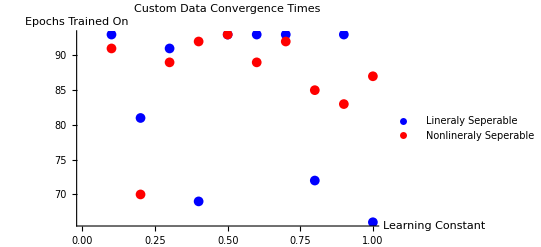

```mathematica
data={{.1,93,91},{.2,81,70},{.3,91,89},{.4,69,92},{.5,93,93},{.6,93,89},{.7,93,92},{.8,72,85},{.9,93,83},{1,66,87}};
ListPlot[{Transpose[{Transpose[data][[1]],Transpose[data][[2]]}],Transpose[{Transpose[data][[1]],Transpose[data][[3]]}]}, AxesLabel->{Style["Learning Constant", Black],Style["Epochs Trained On", Black]}, PlotLabel->Style["Custom Data Convergence Times", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Lineraly Seperable", "Nonlineraly Seperable"}]
```

### Part 4

#### Question

4. (10%) Graph the instances and decision line for the two cases above (with LR=.1). For all graphs always label the axes!

#### Response

The below plots show the two different solutions to the above ARFF files.

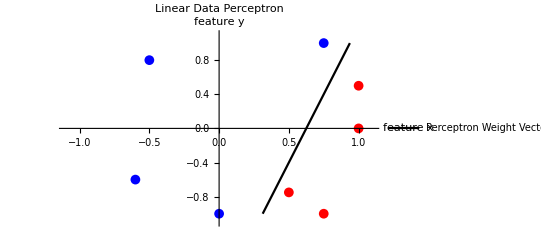

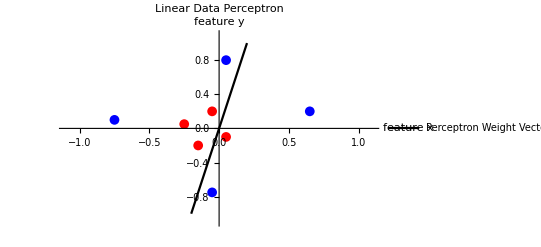

```mathematica
Show[
plotBinaryPerceptronData[{{{-.6,-.6},{-.5,.8},{0,-1},{.75,1}},{{1,0},{.5,-.75},{1,.5},{.75,-1}}}],
plotBinaryPerceptronLine[-0.16,0.05000000000000001,0.1]
]
Show[
plotBinaryPerceptronData[{{{.05,.8},{.65,.2},{-.05,-.75},{-.75,.1}},{{-.05,.2},{-.25,.05},{-.15, -.2},{.05,-.1}}}],
plotBinaryPerceptronLine[-0.05000000000000002,0.009999999999999995,0.0]
]
```

### Part 5

#### Question

5. (20%) Use the perceptron rule to learn this version of the voting task.  This particular task is an edited version of the standard voting set, where we have replaced all the “don’t know” values with the most common value for the particular attribute.  Randomly split the data into 70% training and 30% test set.  Try it five times with different random 70/30 splits.  For each split report the final training and test set accuracy and the # of epochs required.  Also report the average of these values from the 5 trials.  You should update after every instance.  Remember to shuffle the data order after each epoch.  By looking at the weights, explain what the model has learned and how the individual input features affect the result.  Which specific features are most critical for the voting task, and which are least critical?  Do one graph of the average misclassification rate vs epochs (0th – final epoch) for the training set. In our helps page is some help for doing graphs.  As a rough sanity check, typical Perceptron accuracies for the voting data set are 90%-98%.

#### Response

For a perceptron that is forced to train on all the data we found an accuracy in the 90s.

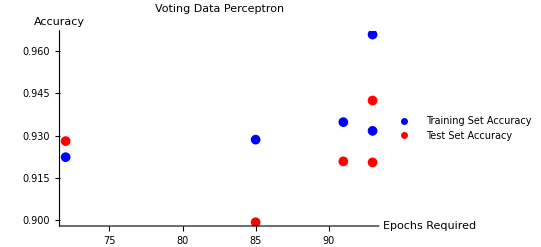

The average amount of epochs trained on was 86.8

The average training accuracy was 0.936646

The average testing accuracy was 0.92223

```mathematica
accuracy = {{85,0.9285714285714286,0.8992805755395683},{93,0.9316770186335404,0.9205035971223022},{72,0.922360248447205,0.9280575539568345},{91,0.9347826086956522,0.920863309352518},{93,0.9658385093167702,0.9424460431654677}};
ListPlot[{Transpose[{accuracy[[All,1]],accuracy[[All, 2]]}],Transpose[{accuracy[[All,1]],accuracy[[All, 3]]}]}, AxesLabel->{Style["Epochs Required", Black],Style["Accuracy", Black]}, PlotLabel->Style["Voting Data Perceptron", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Test Set Accuracy"}]
Print["The average amount of epochs trained on was ", N[Mean[accuracy[[All,1]]]]]
Print["The average training accuracy was ", N[Mean[accuracy[[All,2]]]]]
Print["The average testing accuracy was ", N[Mean[accuracy[[All,3]]]]]
```

For this  data set a good stopping criteria was determined to be when the perceptron reached 5 successive iterations of it’s data set with no significant increase in the weight vector. A significant increase is considered to be when the summed changed in the weight vector is more than 1/2 times the number of features times the training constant.

The final weight vector for a perceptron with a test accuracy of 96 % is shown below:
{0.0, 0.47336482815648373, 1.1834120703912094, -1.6567768985476934, 0.0, 0.23668241407824187, -0.23668241407824187, -0.23668241407824187, 0.9467296563129675, -0.47336482815648373, 0.7100472422347256, -0.47336482815648373, 0.47336482815648373, -0.23668241407824187, 0.9467296563129675, -0.23668241407824187, 0.47336482815648373}
According to this data, there is a slight offset (bias) in the data. Moreover, the 3rd and 4th features seem to be the most influential with the 1st and 5th features being least influential. It’s important to note that not all returned weight vectors had a bias. The most-accurate ones all did though. Note that the longer the perceptron was allowed to train the more accurate it tended to be. This is best shown by the upward-sloping trend in the above plot.
Most influential features: 3, 4
Least Influential features: 1, 5

### Part 6

#### Question

6.  (15%) Do your own experiment with either the perceptron or delta rule.  Include in your discussion what you learned from the experiment.  Have fun and be creative!  For this lab and all the future labs make sure you do something more than just try out the model on different data sets.  One option you can do to fulfill this part is the following:

Use the perceptron rule to learn the iris task or some other task with more than two possible output values. Note that the iris data set has 3 output classes, and a perceptron node only has two possible outputs.  Two common ways to deal with this are:

a)  Create 1 perceptron for each output class.  Each perceptron has its own training set which considers its class positive and all other classes to be negative examples.  Run all three perceptrons on novel data and set the class to the label of the perceptron which outputs high.  If there is a tie, choose the perceptron with the highest net value.

b)  Create 1 perceptron for each pair of output classes, where the training set only contains examples from the 2 classes.  Run all perceptrons on novel data and set the class to the label with the most wins (votes) from the perceptrons.  In case of a tie, use the net values to decide.

You could implement one of these.  For either of these approaches you can train up the models independently or simultaneously.  For testing you just execute the novel instance on each model and combine the overall results to see which output class wins.

#### Response

For this part I created two different perceptrons to solve the iris data set. The two perceptrons are the same as described in the problem statement. The perceptron described in part (a) is called a individual-test perceptron. The perceptron described in part (b) is called the matched-pairs perceptron. Each implementation can be found in the code included in the submission of this project.

Each perceptron was allowed to train on 70% of the data and then test the remaining 30%. Only one epoch was used in order to demonstrate baseline viability. Stopping criteria was found not to affect the overall results and so was not included for consistency.

As shown by the data, the matched pairs perceptron achieved a higher and more stable accuracy compared to the individual perceptron model. In fact, it would appear as if in almost every case the matched pairs model performed better than the individual comparing model. Average accuracy is included for reference.

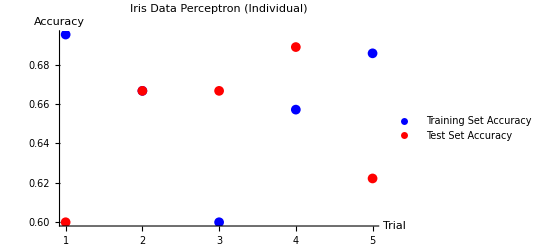

The average training accuracy was 0.660952

The average testing accuracy was 0.648889

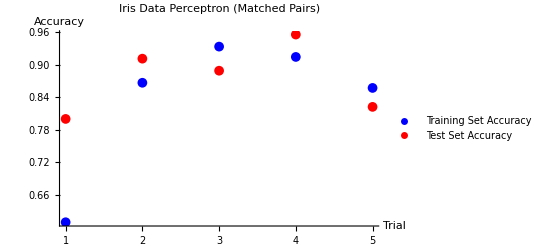

The average training accuracy was 0.83619

The average testing accuracy was 0.875556

```mathematica
IndividualAccuracy = {{1,0.6952380952380952,0.6},{2,0.6666666666666666,0.6666666666666666},{3,0.6,0.6666666666666666},{4,0.6571428571428571,0.6888888888888889},{5,0.6857142857142857,0.6222222222222222}};
matchedPairsAccuracy = {{1,0.6095238095238096,0.8},{2,0.8666666666666667,0.9111111111111111},{3,0.9333333333333333,0.8888888888888888},{4,0.9142857142857143,0.9555555555555556},{5,0.8571428571428571,0.8222222222222222}};
ListPlot[{Transpose[{IndividualAccuracy[[All,1]],IndividualAccuracy[[All, 2]]}],Transpose[{IndividualAccuracy[[All,1]],IndividualAccuracy[[All, 3]]}]}, AxesLabel->{Style["Trial", Black],Style["Accuracy", Black]}, PlotLabel->Style["Iris Data Perceptron (Individual)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Test Set Accuracy"}]
Print["The average training accuracy was ", N[Mean[IndividualAccuracy[[All,2]]]]]
Print["The average testing accuracy was ", N[Mean[IndividualAccuracy[[All,3]]]]]
ListPlot[{Transpose[{matchedPairsAccuracy[[All,1]],matchedPairsAccuracy[[All, 2]]}],Transpose[{matchedPairsAccuracy[[All,1]],matchedPairsAccuracy[[All, 3]]}]}, AxesLabel->{Style["Trial", Black],Style["Accuracy", Black]}, PlotLabel->Style["Iris Data Perceptron (Matched Pairs)", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Test Set Accuracy"}]
Print["The average training accuracy was ", N[Mean[matchedPairsAccuracy[[All,2]]]]]
Print["The average testing accuracy was ", N[Mean[matchedPairsAccuracy[[All,3]]]]]
```